```mathematica
initialSeedPoly[exp_,x_]:=Expand[exp/.{x->(x-Coefficient[exp,x^(Exponent[exp,x]-1)]/Exponent[exp,x])}];
stageTwoSeedPoly[exp_,x_]:=Expand[x^Exponent[exp,x]+Sum[-Abs[Coefficient[exp,x^i]]x^i,{i,1,Exponent[exp,x]-2}]-Abs[exp-Sum[Coefficient[exp,x^i]x^i,{i,1,Exponent[exp,x]}]]];
initialSeed[exp_,x_]:=
Block[
{n,exp1,i,c1},
i=0;
n =Exponent[exp,x];
c1=Coefficient[exp,x^(n-1)];
exp1=stageTwoSeedPoly[initialSeedPoly[exp,x],x];
While[
Not[And[(exp1/.x->i)≤0,(exp1/.x->i+1)≥0]],
i=i+1;
];
Return[Table[-c1/n+Round[i+1]Exp[I*(2Pi/n*(k-1)+Pi/2/n)],{k,1,n}]];
];
PACARootFinder[exp_,x_]:=If[
Exponent[exp,x]==1,
-(exp-x Coefficient[exp,x])/Coefficient[exp,x],
Block[
{n1,z,z1,i,flag},
n1=Exponent[exp,x];
z =N[initialSeed[exp,x]];
While[True,
z1 = Table[z[[i]]+(exp/.x->z[[i]])/((exp/.x->z[[i]])*Sum[If[k≠i,1/(z[[i]]-z[[k]]),0],{k,1,n1}]-(D[exp,x]/.x->z[[i]])),{i,1,n1}];
flag=True;
For[i=1,i≤n1,i++,flag=And[flag,Abs[z[[i]]-z1[[i]]]<0.01]];
If[flag,Break[]];
For[i=1,i≤n1,i++,z[[i]]=z1[[i]]];
];
Return[Round[z1,0.000001]];
]];
NewPACARootFinder[exp_,x_]:=
Block[
{n,cp,exp1,exp2,exp3,c0},
n=Exponent[exp,x];
cp=Coefficient[exp,x^n];
exp1=N[Expand[exp/cp]];
c0=exp1/.x->0;
(*Refining the coefficients*)
exp2=If[Abs[c0]<0.01,Sign[Re[c0]]0.01+I Sign[Im[c0]]0.01,Round[c0,0.01]]+Sum[ If[Abs[Coefficient[exp1,x^i]]<0.01,Sign[Re[Coefficient[exp1,x^i]]]0.01+I Sign[Im[Coefficient[exp1,x^i]]]0.01,Round[Coefficient[exp1,x^i] ,0.01]]*x^i,{i,1,n}];
cp=Coefficient[exp2,x^n];
exp3=N[Expand[exp2/cp]];
Return[PACARootFinder[exp3,x]]
];
xp[exp_,x_]:=Block[
{exp1,n,slnroot,i,m,r,im},
exp1=Numerator[Together[exp]];
n=Exponent[exp1,x];
slnroot = NewPACARootFinder[exp1,x];
m = 0;
For[i=1,i≤n,i++,
r=Re[slnroot[[i]]];
im=Abs[Im[slnroot[[i]]]];
If[im<10^(-3)&&m<r,m =r];
];
Return[m]
];
padZero[S_,j_]:=
Block[
{k,l,y},
If[Length[S]<j+2,
Do[
y=S;
l=Length[S];
For[k=1,k≤j+2-l,k++,AppendTo[y,0]];
,1]
];
Return[y];
];
aExpression[n_,exp_,x_,W_,ω_,β_]:=
Block[
{S,T,U,S1,T1,U1,F,k,root,dexp,p,q,r,R},
root =xp[exp,x];
dexp=D[exp,x];
R=Table[1,{k,1,n+1}];
S=N[CoefficientList[Series[x^4 exp,{x,root,n}],x]];S1=padZero[S,n];
T=N[CoefficientList[Series[-2 exp root x^3+2 exp x^4-dexp root x^4+dexp x^5-2 ⅈ root x ω+2 ⅈ x^2 ω,{x,root,n}],x]];T1=padZero[T,n];
U=N[CoefficientList[Series[-root^2 W-root^2 W^2+2 root W x+2 root W^2 x-W x^2-W^2 x^2+dexp root^2 x^5 β-2 dexp root x^6 β+dexp x^7 β,{x,root,n}],x]];U1=padZero[U,n];
q=S1[[1]];r=T1[[1]];
F=Table[Table[l(l-1)S1[[k-l+1]]+l T1[[k-l+1]]+U1[[k-l+1]],{l,1,k-1}],{k,1,n+1}];
p=Table[-1/(k*(k-1)q+k r ),{k,2,n+1}];
For[k=2,k≤n+1,k++,
R[[k]]= Sum[R[[l]]F[[k]][[l]],{l,1,k-1}];
R[[k]]=Simplify[p [[k-1]]R[[k]]];
];
Return[R]
];
PACAGetModes[m_,exp_,x_,W_,β_]:=
Block[
{exp1,CoeffList,RootCalc,ω,s,root,r},
root=xp[exp,x];
CoeffList=aExpression[m,exp,x,W,ω,β];
RootCalc=Table[(-root)^(n-1),{n,1,m+1}];
exp1=Sum[CoeffList[[n]]RootCalc[[n]],{n,1,m+1}];
s=Numerator[Together[exp1]];
r=NewPACARootFinder[s,ω];
Return[r]
];
PACAPlotModes[m_,exp_,x_,W_,β_]:= ListPlot[(Tooltip[{Re[#1],Abs[Im[#1]]}]&)/@PACAGetModes[m,exp,x,W,β],AspectRatio->1,AspectRatio->{Re[ω],Im[ω]}];
PACATableModes[m_,exp_,x_,W_,β_]:=
Block[
{modes,rearrange},
modes=PACAGetModes[m,exp,x,W,β];
rearrange=Table[{Re[modes[[k]]],Im[modes[[k]]]},{k,1,m}];
Return[TableForm[rearrange,TableHeadings->{Range[m],{"ωR","ωI"}}]]
];
PACAShowModes[m_,exp_,x_,W_,β_]:=Print[Show[PACAPlotModes[m,exp,x,W,β],ImageSize->Large],"\t",PACATableModes[m,exp,x,W,β]]
```

```mathematica
Sqrt[PACAGetModes[45,1-2 x^2+0.4x^3,x,3,0]]
```

{0.904725-0.424415 ⅈ,0.883881-0.351451 ⅈ,0.8586-0.298047 ⅈ,0.833763-0.239673 ⅈ,0.761838-0.119832 ⅈ,0.715098-0.0609315 ⅈ,0.660257-0.0023771 ⅈ,0.596292+0.0563374 ⅈ,0.43768+0.181928 ⅈ,0.0563321+0.596285 ⅈ,0.179358-0.801392 ⅈ,0.801392-0.179358 ⅈ,0.5222+0.116672 ⅈ,0.345964+0.257605 ⅈ,0.181928+0.43768 ⅈ,0.116672+0.5222 ⅈ,0.00236196-0.660256 ⅈ,0.0609315-0.715098 ⅈ,0.119832-0.761838 ⅈ,0.239673-0.833763 ⅈ,0.298048-0.858599 ⅈ,0.351446-0.883885 ⅈ,0.424414-0.904716 ⅈ,0.44725-0.93853 ⅈ,0.534763-0.93157 ⅈ,0.542562-1.08708 ⅈ,0.67338-1.27104 ⅈ,0.563501-0.802487 ⅈ,0.93284-1.47753 ⅈ,0.640604-0.92937 ⅈ,0.257605+0.345964 ⅈ,1.336-1.336 ⅈ,1.68063-1.68063 ⅈ,0.639186-0.734247 ⅈ,2.45153-2.45153 ⅈ,1.54862-1.54862 ⅈ,0.707094-0.707094 ⅈ,0.802469-0.563431 ⅈ,0.929504-0.640675 ⅈ,1.47753-0.93284 ⅈ,0.931829-0.534769 ⅈ,1.27104-0.67338 ⅈ,1.08709-0.542563 ⅈ,0.938576-0.447254 ⅈ,0.734202-0.639177 ⅈ}

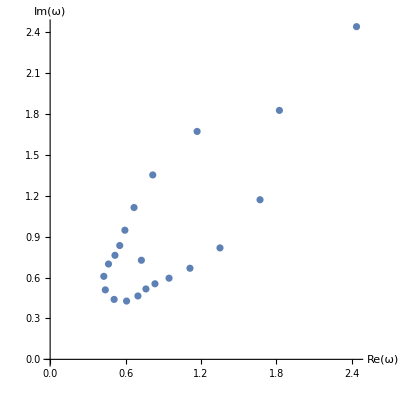

```mathematica
Show[ 
ListPlot[(Tooltip[{Re[#1],Abs[Im[#1]]}]&)/@Sqrt[PACAGetModes[21,1-2 x^2+0.1 x^3,x,3,0]],AspectRatio->1,AxesLabel->{Re[ω],Im[ω]},AxesOrigin->{0,0}],
ListPlot[(Tooltip[{-Re[#1],Abs[Im[#1]]}]&)/@Sqrt[PACAGetModes[21,1-2 x^2+0.1 x^3,x,3,0]],AspectRatio->1,AxesLabel->{Re[ω],Im[ω]},AxesOrigin->{0,0}]
]
```

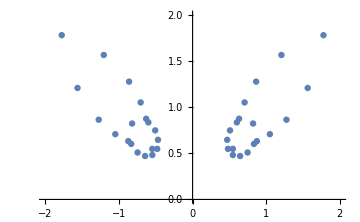
-Graphics-q=0.1

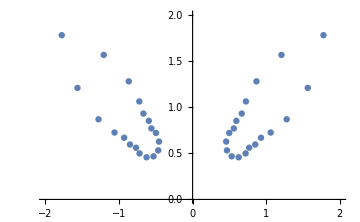
-Graphics-q=0.2

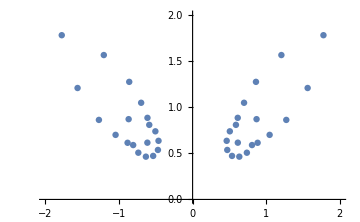
-Graphics-q=0.3

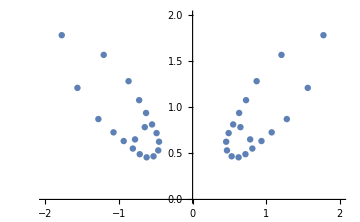
-Graphics-q=0.4

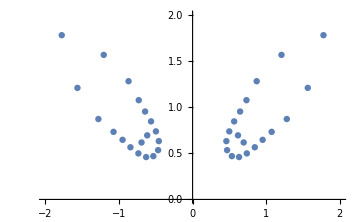
-Graphics-q=0.5

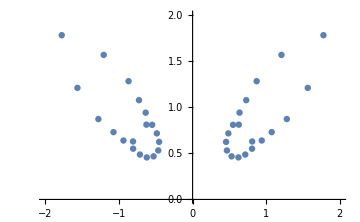
-Graphics-q=0.6

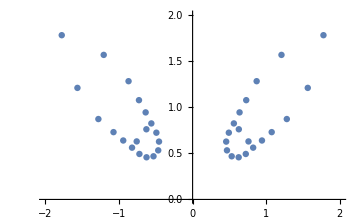
-Graphics-q=0.7

-Graphics-q=0.8

-Graphics-q=0.9

```mathematica
For[
q1=0.1,q1≤0.9,q1=q1+0.1,
Print[Show[
ListPlot[(Tooltip[{Re[#1],-Im[#1]}]&)/@Sqrt[PACAGetModes[20,1-μ x^2+Q x^(2β)/.{μ->2,β->3/2,Q->q1},x,3,0]]],
ListPlot[(Tooltip[{-Re[#1],-Im[#1]}]&)/@Sqrt[PACAGetModes[20,1-μ x^2+Q x^(2β)/.{μ->2,β->3/2,Q->q1},x,3,0]]],
PlotRange->{{-2,2},{0,2}},AxesOrigin->{0,0},ImageSize->Medium
],"q=",q1]
]
```

```mathematica
Clear[l];
l=Re[Sqrt[PACAGetModes[20,1-2x^2+0.4x^3,x,3,0]]];
StandardDeviation[l]
```

0.511348

```mathematica
Mean[Im[Sqrt[PACAGetModes[20,1-μ x^2+Q x^(2β)/.{μ->2,β->3/2,Q->0.1},x,3,0]]]]
```

-0.93022

{0.699569-0.587797 ⅈ,0.699559-0.587799 ⅈ,0.699565-0.5878 ⅈ,0.699566-0.587795 ⅈ,0.699562-0.587797 ⅈ,0.69956-0.587803 ⅈ,0.699563-0.587801 ⅈ,0.699564-0.587796 ⅈ,0.699567-0.587795 ⅈ}

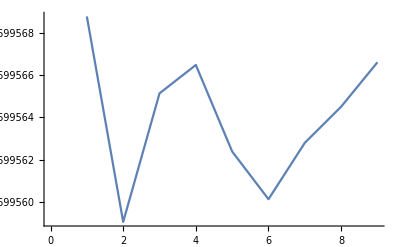

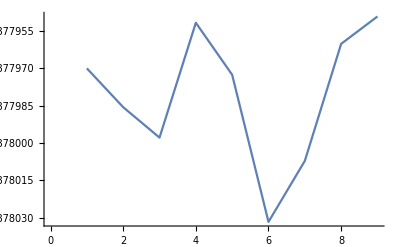

```mathematica
w=Table[Mean[Sqrt[PACAGetModes[45,1-2 x^2+q x^3,x,3,0]]],{q,0.1,0.9,0.1}];
Print[w]
ListLinePlot[Re[w]]
ListLinePlot[Im[w]]
```

```mathematica
start = AbsoluteTime[];
NewPACARootFinder[Sum[RandomReal[{1,23}]*x^i,{i,0,60}],x]
end=AbsoluteTime[];
end-start
```

{1.00431+0.10501 ⅈ,0.875157+0.392734 ⅈ,0.976011+0.220241 ⅈ,0.936513+0.321102 ⅈ,0.852815+0.438723 ⅈ,0.80252+0.550464 ⅈ,0.760235+0.630734 ⅈ,0.658952+0.764014 ⅈ,0.605837+0.821003 ⅈ,0.478159+0.866397 ⅈ,0.569957+1.016 ⅈ,0.358041+0.951645 ⅈ,0.225536+0.960639 ⅈ,-0.040834+0.930753 ⅈ,0.079568+1.09412 ⅈ,-0.000279+1.08714 ⅈ,-0.146302+1.08613 ⅈ,-0.223236+0.934008 ⅈ,-0.351659+0.911228 ⅈ,-0.571857+0.769707 ⅈ,-0.548254+1.03847 ⅈ,-0.526279+0.808799 ⅈ,-0.664215+0.767672 ⅈ,-0.760872+0.61864 ⅈ,-0.844858+0.542425 ⅈ,-0.865675+0.440984 ⅈ,-0.883797+0.364872 ⅈ,-0.943115+0.278228 ⅈ,-0.990628+0.13649 ⅈ,-0.951754+0.009675 ⅈ,-0.951754-0.009675 ⅈ,-0.990628-0.13649 ⅈ,-0.943115-0.278228 ⅈ,-0.883797-0.364872 ⅈ,-0.865675-0.440984 ⅈ,-0.844858-0.542425 ⅈ,-0.760872-0.61864 ⅈ,-0.571857-0.769707 ⅈ,-0.664215-0.767672 ⅈ,-0.526279-0.808799 ⅈ,-0.548254-1.03847 ⅈ,-0.351659-0.911228 ⅈ,-0.223236-0.934008 ⅈ,-0.146302-1.08613 ⅈ,-0.040834-0.930753 ⅈ,-0.000279-1.08714 ⅈ,0.079568-1.09412 ⅈ,0.225536-0.960639 ⅈ,0.358041-0.951645 ⅈ,0.478159-0.866397 ⅈ,0.569957-1.016 ⅈ,0.605837-0.821003 ⅈ,0.658952-0.764014 ⅈ,0.760235-0.630734 ⅈ,0.80252-0.550464 ⅈ,0.852815-0.438723 ⅈ,0.875157-0.392734 ⅈ,0.936513-0.321102 ⅈ,0.976011-0.220241 ⅈ,1.00431-0.10501 ⅈ}

0.984108

```mathematica
start = AbsoluteTime[];
NewPACARootFinder[x^5-9x+70,x]
end=AbsoluteTime[];
end-start
start = AbsoluteTime[];
NSolve[x^5-9x+70==0,x]
end=AbsoluteTime[];
end-start
```

{1.85179+1.23265 ⅈ,-0.615964+2.31164 ⅈ,-2.47166,-0.615964-2.31164 ⅈ,1.85179-1.23265 ⅈ}

0.002

{{x→-2.47166},{x→-0.615964-2.31164 ⅈ},{x→-0.615964+2.31164 ⅈ},{x→1.85179-1.23266 ⅈ},{x→1.85179+1.23266 ⅈ}}

0.00211